```mathematica
ClearAll["Global`*"]
(* set your home directory *)
SetDirectory[NotebookDirectory[]];
```

```mathematica
(* import nodes and triangles *)
nodes=Import["n.dat","Table"];
triangles=Import["t.dat","Table"];
(* Mathematica counts from 1 not 0 *)
triangles+=1;
```

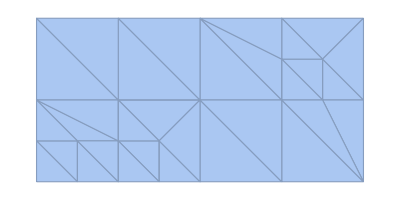

```mathematica
(* our triangulation *)
𝒦=MeshRegion[nodes,Triangle[triangles]]
```